(((-0.1+Cos[theta])^2-0.333333 (-0.1+Sin[theta])^2) (-0.1+Sin[theta]))/(-0.1+Cos[theta])^3

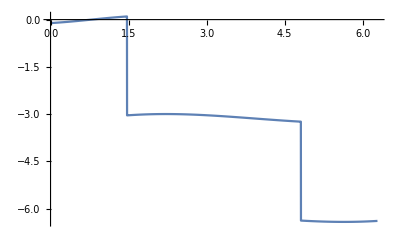

```mathematica
xs=0;
ys=0;
xd=0.1;
r0=1;
BH1=r0 Cos[theta]+xs Cos[theta]+ys Sin[theta]-xd;
BH2=r0 Sin[theta]+xs Cos[theta]+ys Sin[theta]-xd;
x=BH2/BH1;
kotmerjeni=ArcTan[x];

serija=x-x^3/3;
Simplify[serija]
zaplot=Simplify[TrigReduce[serija]];

Plot[kotmerjeni-theta,{theta,0,Pi 2}]
```